## Chapter 5 Problem 24: Fine structure w/Zeeman in hydrogen

```mathematica
Remove["Global`*"]
```

```mathematica
$Assumptions={A>0,B>0,s∈ Reals}
```

{A>0,B>0,s∈ℝ}

```mathematica
{A∈Reals,B∈Reals,sj∈Reals,ss∈Reals}
```

{A∈ℝ,B∈ℝ,sj∈ℝ,ss∈ℝ}

Write the formula (derived in the solutions) for the diagonal and off diagonal matrix elements

```mathematica
diag=(A/2)(j(j+1)-l(l+1)-3/4)+B(1+sj/(2l+1))m;
```

```mathematica
offd=-B/(2l+1)Sqrt[(l+1/2)^2-m^2];
```

Evaluate the first order energy shifts for the four states that are diagonal in the perturbation

```mathematica
Δ01p1=diag/.{l->0,j->1/2,sj->1,m->1/2}
```

B

```mathematica
Δ01m1=diag/.{l->0,j->1/2,sj->1,m->-1/2}
```

-B

```mathematica
Δ13p3=diag/.{l->1,j->3/2,sj->1,m->3/2}
```

A/2+2 B

```mathematica
Δ13m3=diag/.{l->1,j->3/2,sj->1,m->-3/2}
```

A/2-2 B

The 2x2 sub-matrices that mix are for l=1 and m=1/2 or m=-1/2, with off diagonal elements mixing j=1/2 (sj=-1) and j=3/2 (sj=1).

```mathematica
diag1=diag/.{l->1,j->1/2,sj->-1,m->ss/2}
diag3=diag/.{l->1,j->3/2,sj->1,m->ss/2}
diagx=offd/.{l->1,m->1/2}
```

-A+(B ss)/3

A/2+(2 B ss)/3

-(√2 B)/3

Diagonalize to get the eigenvalues that are the first order energy shifts

```mathematica
eivs=Eigenvalues[{{diag1,diagx},{diagx,diag3}}];
```

```mathematica
Δp1=Simplify[eivs/.ss->1][[1]]
```

1/4 (-A+2 B-√(9 A^2+4 A B+4 B^2))

```mathematica
Δp2=Simplify[eivs/.ss->1][[2]]
```

1/4 (-A+2 B+√(9 A^2+4 A B+4 B^2))

```mathematica
Δm1=Simplify[eivs/.ss->-1][[1]]
```

1/4 (-A-2 B-√(9 A^2-4 A B+4 B^2))

```mathematica
Δm2=Simplify[eivs/.ss->-1][[2]]
```

1/4 (-A-2 B+√(9 A^2-4 A B+4 B^2))

Plot as a function of B/A

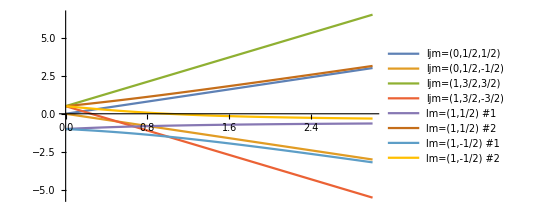

```mathematica
Δvals=Simplify[({Δ01p1,Δ01m1,Δ13p3,Δ13m3,Δp1,Δp2,Δm1,Δm2}/.B->β A)/A];
Plot[Δvals,{β,0,3},AspectRatio->0.55,
PlotLegends->{"ljm=(0,1/2,1/2)","ljm=(0,1/2,-1/2)","ljm=(1,3/2,3/2)","ljm=(1,3/2,-3/2)","lm=(1,1/2) #1","lm=(1,1/2) #2","lm=(1,-1/2) #1","lm=(1,-1/2) #2"}]
```